# Group theory

```mathematica
Jp[j_,m1_,m2_]:=Sqrt[(j+m1+1)(j-m1)/2]KroneckerDelta[m2,m1+1]
Jm[j_,m1_,m2_]:=Sqrt[(j+m1)(j-m1+1)/2]KroneckerDelta[m2,m1-1]
```

```mathematica
j=2
J1=Table[(Jp[j,j+1-l,j+1-k]+Jm[j,j+1-l,j+1-k])/Sqrt[2] ,{k,2j+1},{l,2j+1}];
J2=Table[(Jp[j,j+1-l,j+1-k]-Jm[j,j+1-l,j+1-k])/(Sqrt[2] I),{k,2j+1},{l,2j+1}];
J3=Table[(j-m+1) KroneckerDelta[m,n],{m,2j+1},{n,2j+1}];
J={J1,J2,J3};
```

2

```mathematica
σtot=Sum[Tr[(J[[a]].J[[b]]+J[[b]].J[[a]]).(J[[a]].J[[b]]+J[[b]].J[[a]])],{a,1,3},{b,1,3}]

σ0=1/(2j+1)Sum[Tr[J[[a]].J[[b]]+J[[b]].J[[a]]]^2,{a,1,3},{b,1,3}]

σ1=1/Tr[J[[1]].J[[1]]]Sum[Tr[J[[c]](J[[a]].J[[b]]+J[[b]].J[[a]])]^2,{a,1,3},{b,1,3},{c,1,3}]
```

660

240

0

```mathematica
dR=(2j+1);

asing=Sum[Sum[Abs[Tr[J[[a]].J[[b]]]]^2,{a,1,3}],{b,1,3}]/Tr[J[[1]].J[[1]]]/dR
atot=Sum[Sum[Tr[(J[[a]].J[[b]]+J[[b]].J[[a]]).(J[[a]].J[[b]]+J[[b]].J[[a]])],{a,1,3}],{b,1,3}]/Tr[J[[1]].J[[1]]]/4;
asymm=atot-asing

bsing=Sum[Sum[Abs[Sum[Sum[Tr[J[[a]].J[[b]].J[[c]]]Tr[J[[d]].(J[[a]].J[[c]]-J[[c]].J[[a]])]/Tr[J[[1]].J[[1]]],{a,1,3}],{c,1,3}]]^2,{b,1,3}],{d,1,3}]/Tr[J[[1]].J[[1]]]/dR

btot=-Sum[Sum[Sum[Sum[Sum[Sum[Tr[J[[a]].J[[b]].J[[c]].J[[f]].J[[b]].J[[e]]]Tr[J[[d]].(J[[a]].J[[c]]-J[[c]].J[[a]])]Tr[J[[d]].(J[[e]].J[[f]]-J[[f]].J[[e]])]/Tr[J[[1]].J[[1]]]^2,{a,1,3}],{b,1,3}],{c,1,3}],{d,1,3}],{e,1,3}],{f,1,3}]/Tr[J[[1]].J[[1]]];

bsymm=btot-bsing
```

6

21/2

6

42

```mathematica
K1=dR CR^2
K2=K1-dAdj IAdj IR/2
Ksing=4 IR^2/dR dAdj
Ksymm=FullSimplify[2 K1+2 K2-Ksing]
ratio=FullSimplify[Ksymm/Ksing]
```

CR^2 dR

CR^2 dR-(dAdj IAdj IR)/2

(4 dAdj IR^2)/dR

4 CR^2 dR-(dAdj IR (dR IAdj+4 IR))/dR

-1+(CR^2 dR^2)/(dAdj IR^2)-(dR IAdj)/(4 IR)

## SU(2)

```mathematica
dR=n
dAdj=3
IAdj=2
IR=n/12(n^2-1);
CR=FullSimplify[j(j+1)/.j->(n-1)/2]
Simplify[Ksing]
Simplify[Ksymm]
Simplify[ratio]
```

n

3

2

1/4 (-1+n^2)

1/12 n (-1+n^2)^2

1/6 n (4-5 n^2+n^4)

(-1+n^2)/(2 (-4+n^2))

## gluinos

```mathematica
Com[A_,B_]:=l[A].l[B]-l[B].l[A];
ACom[A_,B_]:=l[A].l[B]+l[B].l[A];
l[1]={{0,1,0},{1,0,0},{0,0,0}};
l[2]={{0,-I,0},{I,0,0},{0,0,0}};
l[3]={{1,0,0},{0,-1,0},{0,0,0}};
l[4]={{0,0,1},{0,0,0},{1,0,0}};
l[5]={{0,0,-I},{0,0,0},{I,0,0}};
l[6]={{0,0,0},{0,0,1},{0,1,0}};
l[7]={{0,0,0},{0,0,-I},{0,I,0}};
l[8]={{1,0,0},{0,1,0},{0,0,-2}}/Sqrt[3];

Do[f[i,j,k]=-I Tr[l[i].Com[j,k]]/4;
d[i,j,k]=Tr[l[i].ACom[j,k]]/4;,{k,8},{j,8},{i,8}];
```

```mathematica
T8[m_]:=-I Table[f[m,i,j] ,{i,8},{j,8}]
C1S=IdentityMatrix[8]/Sqrt[8];
C8A[m_]:=Table[f[m,i,j] ,{i,8},{j,8}]/Sqrt[3];
C8S[m_]:=Table[d[m,i,j] ,{i,8},{j,8}]/Sqrt[5/3];
```

```mathematica
S1to8A=FullSimplify[Sum[(1/2 Tr[C8A[e].(C1S.T8[b]+T8[b].C1S)]-I γ Sum[Tr[C8A[e].T8[c1].C1S.T8[d1]]f[b,c1,d1],{c1,1,8},{d1,1,8}])*(1/2 Tr[C8A[e].(C1S.T8[b]+T8[b].C1S)]-I γ Sum[Tr[C8A[e].T8[c2].C1S.T8[d2]]f[b,c2,d2],{c2,1,8},{d2,1,8}])*,{b,1,8},{e,1,8}], Element[γ, Reals]]

S8toS1=FullSimplify[Sum[(1/2 Tr[C1S.(C8S[e].T8[b]+T8[b].C8S[e])]-I γ Sum[Tr[C1S.T8[c].C8S[e].T8[d]]f[b,c1,d1],{c1,1,8},{d1,1,8}])*(1/2 Tr[C1S.(C8S[e].T8[b]+T8[b].C8S[e])]-I γ Sum[Tr[C1S.T8[c2].C8S[e].T8[d2]]f[b,c2,d2],{c2,1,8},{d2,1,8}])*,{b,1,8},{e,1,8}], Element[γ, Reals]]

A8toS8=FullSimplify[Sum[(1/2 Tr[C8S[a].(C8A[e].T8[b]+T8[b].C8A[e])]-I γ Sum[Tr[C8S[a].T8[c1].C8A[e].T8[d1]]f[b,c1,d1],{c1,1,8},{d1,1,8}])*(1/2 Tr[C8S[a].(C8A[e].T8[b]+T8[b].C8A[e])]-I γ Sum[Tr[C8S[a].T8[c2].C8A[e].T8[d2]]f[b,c2,d2],{c2,1,8},{d2,1,8}])*,{a,1,8},{b,1,8},{e,1,8}], Element[γ, Reals]]
```

3/4 (2+3 γ)^2

0

6

```mathematica
S1toAll=FullSimplify[Sum[Tr[(1/2(C1S.T8[b]+T8[b].C1S)-I γ Sum[T8[c1].C1S.T8[d1]f[b,c1,d1],{c1,1,8},{d1,1,8}]).ConjugateTranspose[1/2(C1S.T8[b]+T8[b].C1S)-I γ Sum[T8[c2].C1S.T8[d2]f[b,c2,d2],{c2,1,8},{d2,1,8}]]],{b,1,8}], Element[γ, Reals]]
S8toAll=FullSimplify[Sum[Tr[(1/2(C8S[e].T8[b]+T8[b].C8S[e])-I γ Sum[T8[c1].C8S[e].T8[d1]f[b,c1,d1],{c1,1,8},{d1,1,8}]).ConjugateTranspose[1/2(C8S[e].T8[b]+T8[b].C8S[e])-I γ Sum[T8[c2].C8S[e].T8[d2]f[b,c2,d2],{c2,1,8},{d2,1,8}]]],{b,1,8},{e,1,8}], Element[γ, Reals]]

A8toAll=FullSimplify[Sum[Tr[(1/2(C8A[e].T8[b]+T8[b].C8A[e])-I γ Sum[T8[c1].C8A[e].T8[d1]f[b,c1,d1],{c1,1,8},{d1,1,8}]).ConjugateTranspose[1/2(C8A[e].T8[b]+T8[b].C8A[e])-I γ Sum[T8[c2].C8A[e].T8[d2]f[b,c2,d2],{c2,1,8},{d2,1,8}]]],{b,1,8},{e,1,8}], Element[γ, Reals]]
```

3/4 (2+3 γ)^2

9 (2+γ (4+3 γ))

9 (2+γ (4+7 γ))

```mathematica
Simplify[S1toAll-S1to8A]
Simplify[S8toAll-A8toS8]
Simplify[A8toAll-A8toS8-3/4 (2-3 γ)^2]
```

0

3 (2+3 γ)^2

9/4 (2+5 γ)^2

## squarks

```mathematica
C3A[m_]:= Table[LeviCivitaTensor[3][[m,i,j]] ,{i,3},{j,3}]/Sqrt[2]
T1=1/2({{0, 1, 0}, {1, 0, 0}, {0, 0, 0}});T2=1/2({{0, -I, 0}, {I, 0, 0}, {0, 0, 0}});T3=1/2({{1, 0, 0}, {0, -1, 0}, {0, 0, 0}});T4=1/2({{0, 0, 1}, {0, 0, 0}, {1, 0, 0}});T5=1/2({{0, 0, -I}, {0, 0, 0}, {I, 0, 0}});T6=1/2({{0, 0, 0}, {0, 0, 1}, {0, 1, 0}});T7=1/2({{0, 0, 0}, {0, 0, -I}, {0, I, 0}});T8=1/(2Sqrt[3])({{1, 0, 0}, {0, 1, 0}, {0, 0, -2}});

TT={T1,T2,T3,T4,T5,T6,T7,T8};

S3toAll=FullSimplify[Sum[Tr[(1/2(-C3A[e].Transpose[TT[[b]]]+TT[[b]].C3A[e])+I γ Sum[TT[[c1]].C3A[e].Transpose[TT[[d1]]]f[b,c1,d1],{c1,1,8},{d1,1,8}]).ConjugateTranspose[1/2(-C3A[e].Transpose[TT[[b]]]+TT[[b]].C3A[e])+I γ Sum[TT[[c2]].C3A[e].Transpose[TT[[d2]]]f[b,c2,d2],{c2,1,8},{d2,1,8}]]],{b,1,8},{e,1,3}], Element[γ, Reals]]
```

3 (1+γ)^2

## SU(N) fundamental

```mathematica
dR=3
dAdj=8
IR=1/2
CR=(dR^2-1)/(2dR)
IAdj=3
Simplify[Ksing/Ksymm]
ratio
```

3

8

1/2

4/3

3

2/5

2/5

## Quintuplet

```mathematica
Jp[j_,m1_,m2_]:=Sqrt[(j+m1+1)(j-m1)/2]KroneckerDelta[m2,m1+1];
Jm[j_,m1_,m2_]:=Sqrt[(j+m1)(j-m1+1)/2]KroneckerDelta[m2,m1-1];
j=2;
J1=Table[(Jp[j,j+1-l,j+1-k]+Jm[j,j+1-l,j+1-k])/Sqrt[2] ,{k,2j+1},{l,2j+1}];
J2=Table[(Jp[j,j+1-l,j+1-k]-Jm[j,j+1-l,j+1-k])/(Sqrt[2] I),{k,2j+1},{l,2j+1}];
J3=Table[(j-m+1) KroneckerDelta[m,n],{m,2j+1},{n,2j+1}]
J={J1,J2,J3};
i={{0,0,0,0,1},{0,0,0,-1,0},{0,0,1,0,0},{0,-1,0,0,0},{1,0,0,0,0}};

CG1=Table[ClebschGordan[{2,j-3},{2,i-3},{0,0}] ,{i,5},{j,5}].iᵀ ;
CG3[m_]:=Table[ClebschGordan[{2,j-3},{2,i-3},{1,m}] ,{i,5},{j,5}].iᵀ;
CG5[m_]:=Table[ClebschGordan[{2,j-3},{2,i-3},{2,m}] ,{i,5},{j,5}].iᵀ;

σtot1=1/(5 5)Sum[(π α2^2)/m^2 1/4 Tr[CG1.(J[[a]].J[[b]]+J[[b]].J[[a]])]*(Tr[CG1.(J[[a]].J[[b]]+J[[b]].J[[a]])])*,{a,1,3},{b,1,3}]
σtot5=1/(5 5)Sum[(π α2^2)/m^2 1/4 Tr[CG5[m1].(J[[a]].J[[b]]+J[[b]].J[[a]])]*(Tr[CG5[m1].(J[[a]].J[[b]]+J[[b]].J[[a]])])*,{m1,-2,2},{a,1,3},{b,1,3}]
σv00γγ= FullSimplify[(π αem^2)/m^2 1/4 Tr[(Sqrt[S1] √(1/5)CG1-Sqrt[S5] √(2/7)CG5[0]).(J[[a]].J[[b]]+J[[b]].J[[a]])]*(Tr[(Sqrt[S1] √(1/5)CG1-Sqrt[S5] √(2/7)CG5[0]).(J[[a]].J[[b]]+J[[b]].J[[a]])])*/.a->3/.b->3,Assumptions->{S1>0,S5>0}]
σv00γγ= FullSimplify[(π αem^2)/m^2 Sum[1/4 Tr[(Sqrt[S1] √(1/5)CG1-Sqrt[S5] √(2/7)CG5[0]).(J[[a]].J[[b]]+J[[b]].J[[a]])]*(Tr[(Sqrt[S1] √(1/5)CG1-Sqrt[S5] √(2/7)CG5[0]).(J[[a]].J[[b]]+J[[b]].J[[a]])])*,{a,1,2},{b,1,2}],Assumptions->{S1>0,S5>0}]
```

{{2,0,0,0,0},{0,1,0,0,0},{0,0,0,0,0},{0,0,0,-1,0},{0,0,0,0,-2}}

ClebschGordan::phy: ThreeJSymbol[{2, -2}, {2, -2}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, -1}, {2, -2}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 0}, {2, -2}, {0, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

(12 π α2^2)/(5 m^2)

ClebschGordan::phy: ThreeJSymbol[{2, -2}, {2, -2}, {2, 2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, -1}, {2, -2}, {2, 2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 1}, {2, -2}, {2, 2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

(21 π α2^2)/(5 m^2)

ClebschGordan::phy: ThreeJSymbol[{2, -2}, {2, -2}, {2, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, -1}, {2, -2}, {2, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 0}, {2, -2}, {2, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

Part::pkspec1: The expression a cannot be used as a part specification.

Part::pkspec1: The expression b cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

(4 π (S1+S5-2 √(S1 S5)) αem^2)/m^2

ClebschGordan::phy: ThreeJSymbol[{2, -2}, {2, -2}, {2, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, -1}, {2, -2}, {2, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{2, 0}, {2, -2}, {2, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

(2 π (4 S1+S5+4 √(S1 S5)) αem^2)/m^2

# Annihilation

```mathematica
ΓηB=Simplify[α^2 (CJBgg IR)/dB (λf^3 α^3)/(2n^3)mDM]
Γψferm=α^2 IR/12(λf^3 α^3)/(2n^3)mDM
Γψgauge=α^2 IR/24(λf^3 α^3)/(2n^3)mDM 
(*Γη0=α^2 (IR^2 dAdj)/dR(λf^3 α^3)/(2n^3)mDM
Γηsymm=Simplify[α^2 (IR^2 dAdj)/dR(-1+(CR^2 dR^2)/(dAdj IR^2)-(dR IAdj)/(4 IR))]/dsymm  (λf^3 α^3)/(2n^3)mDM*)
```

(3 CJBgg mDM α^5 λf^3)/(2 dB n^3)

(mDM α^5 λf^3)/(8 n^3)

(mDM α^5 λf^3)/(16 n^3)

## quintuplet

```mathematica
dR=5;
IR=n/12(n^2-1)/.n->dR;
Γη1=Simplify[ΓηB/.dB->1/.CJBgg->6/.λf->6]/2
Γη5=Simplify[ΓηB/.dB->5/.CJBgg->21/2/.λf->3]/2
Γψ3=Simplify[3(3+1)Γψferm+ Γψgauge/.λf->5]/2
```

(3240 mDM α^5)/n^3

(567 mDM α^5)/(4 n^3)

(15625 mDM α^5)/(48 n^3)

## wino

```mathematica
dR=3;
IR=n/12(n^2-1)/.n->dR;
Γη1=Simplify[ΓηB/.dB->1/.CJBgg->2/.λf->2]/2
Γψ3=Simplify[3(3+1)Γψferm+ Γψgauge/.λf->1]/2
```

3

(8 mDM α^5)/n^3

(25 mDM α^5)/(48 n^3)

## gluinos

```mathematica
dR=8;
IR=3;
Γη1S=Simplify[ΓηB/.dB->1/.CJBgg->3/.λf->3]/2
Γη8S=Simplify[ΓηB/.dB->8/.CJBgg->6/.λf->3/2]/2
Γψ8A=Simplify[3 2 2Γψferm/.λf->3/2]/2
```

(243 mDM α^5)/(4 n^3)

(243 mDM α^5)/(128 n^3)

(81 mDM α^5)/(32 n^3)

## squark

```mathematica
dR=3;
IR=1/2;
Γη1S=Simplify[ΓηB/.dB->1/.CJBgg->4/3/.λf->4/3]/2
```

(32 mDM α^5)/(81 n^3)

## SU(3) dark

```mathematica
dR=3;
IR=1/2;
Γη1S=3 Simplify[ΓηB/.dB->1/.CJBgg->4/3/.λf->4/3]
```

(64 mDM α^5)/(27 n^3)

# Decays

```mathematica
a10=2/(λf α m)
a21=2/(λi α m)
R10=2/a10^(3/2)Exp[-r/a10];
R21=1/Sqrt[24] 1/a21^(3/2) r/a21 Exp[-r/(2a21)];
Γps=16/9(α k)/m^2(Integrate[R21(CJ D[R10,r]-Cτ α/2  m R10)r^2,{r,0,Infinity}])^2
```

2/(m α λf)

2/(m α λi)

ConditionalExpression[(2048 k α^3 λf^3 (Cτ+CJ λf)^2 λi^5)/(3 (2 λf+λi)^8),Re[m α (2 λf+λi)]>0]

```mathematica
Γps=(2048 αem α^2 λi^5 λf^3)/(3(2λf+λi)^8)(α^2 m)/4(-λi^2/4+λf^2)1/(3 dB)(Cτ/λf+ CJ)^2
```

(512 m α^4 αem (CJ+Cτ/λf)^2 λf^3 λi^5 (λf^2-λi^2/4))/(9 dB (2 λf+λi)^8)

## quintuplet

```mathematica
Γ1=N[Simplify[(512 m α^4 αem  λf^3 λi^5 (λf^2-λi^2/4))/(9 dB (2 λf+λi)^8)(CJ+Cτ/λf)^2/.dB->1/.λi->6/.λf->5/.CJ->√6/.Cτ->√6]]
Γ3=N[FullSimplify[((512 m α^4 αem  λf^3 λi^5 (λf^2-λi^2/4))/(9 dB (2 λf+λi)^8)(CJ+Cτ/λf)^2/.dB->3/.λi->5/.λf->6/.CJ->√6/.Cτ->-√6)+((512 m α^4 αem  λf^3 λi^5 (λf^2-λi^2/4))/(9 dB (2 λf+λi)^8)(CJ+Cτ/λf)^2/.dB->3/.λi->5/.λf->3/.CJ->√(21/2)/.Cτ->√42)]]
Γ5=N[Simplify[(512 m α^4 αem  λf^3 λi^5 (λf^2-λi^2/4))/(9 dB (2 λf+λi)^8)(CJ+Cτ/λf)^2/.dB->5/.λi->3/.λf->5/.CJ->√(21/2)/.Cτ->-√42]]
```

1.77979 m α^4 αem

0.826139 m α^4 αem

0.0364334 m α^4 αem

## wino

```mathematica
Γ1=N[Simplify[(512 m α^4 αem  λf^3 λi^5 (λf^2-λi^2/4))/(9 dB (2 λf+λi)^8)(CJ+Cτ/λf)^2/.dB->1/.λi->2/.λf->1/.CJ->√2/.Cτ->√2]]
Γ3=N[FullSimplify[((512 m α^4 αem  λf^3 λi^5 (λf^2-λi^2/4))/(9 dB (2 λf+λi)^8)(CJ+Cτ/λf)^2/.dB->3/.λi->1/.λf->2/.CJ->√2/.Cτ->-√2)]]
```

0.

0.000728178 m α^4 αem

## gluinos

```mathematica
Γ1S=N[Simplify[(512 m α^5  λf^3 λi^5 (λf^2-λi^2/4))/(3 dB (2 λf+λi)^8)(CJ+Cτ/λf)^2/.dB->1/.λi->3/.λf->3/2/.CJ->√3/.Cτ->√(27/4)]]
Γ8A=N[FullSimplify[((512 m α^5  λf^3 λi^5 (λf^2-λi^2/4))/(3 dB (2 λf+λi)^8)(CJ+Cτ/λf)^2/.dB->3/.λi->3/2/.λf->3/.CJ->√3/.Cτ->-√(27/4))+((512 m α^5  λf^3 λi^5 (λf^2-λi^2/4))/(3 dB (2 λf+λi)^8)(CJ+Cτ/λf)^2/.dB->3/.λi->3/2/.λf->3/2/.CJ->√6/.Cτ->0)]]
Γ8S=N[Simplify[(512 m α^5  λf^3 λi^5 (λf^2-λi^2/4))/(3 dB (2 λf+λi)^8)(CJ+Cτ/λf)^2/.dB->3/.λi->3/2/.λf->3/2/.CJ->√6/.Cτ->0]]
```

0.

0.0951643 m α^5

0.0877915 m α^5

# Integrals

```mathematica
a0=2/(λf α m);
R10=2/a0^(3/2)Exp[-r/a0];
R20=1/Sqrt[2] 1/a0^(3/2)(1-1/2 r/a0)Exp[-r/(2a0)];
R21=1/Sqrt[24] 1/a0^(3/2) r/a0 Exp[-r/(2a0)];

ϕL0=Sqrt[4π]Sqrt[2l+1] Gamma[1+l-I λi ζ]/Gamma[2(l+1)] Exp[π λi ζ/2] Exp[-I p  r] (2 I p r)^l Hypergeometric1F1[1+l+I λi ζ,2(l+1),2 I p r]/.l->0;
ϕL1=Sqrt[4π]Sqrt[2l+1] Gamma[1+l-I λi ζ]/Gamma[2(l+1)] Exp[π λi ζ/2] Exp[-I p  r] (2 I p r)^l Hypergeometric1F1[1+l+I λi ζ,2(l+1),2 I p r]/.l->1;
ϕL2=Sqrt[4π]Sqrt[2l+1] Gamma[1+l-I λi ζ]/Gamma[2(l+1)] Exp[π λi ζ/2] Exp[-I p  r] (2 I p r)^l Hypergeometric1F1[1+l+I λi ζ,2(l+1),2 I p r]/.l->2;

Mps10=FullSimplify[Integrate[ r^2ϕL1(CJ D[R10,r]-(Cτ α m)/2 R10),{r,0,Infinity}]/.p->m α/(2ζ)]
Mps20=FullSimplify[Integrate[ r^2ϕL1(CJ D[R20,r]-(Cτ α m)/2 R20),{r,0,Infinity}]/.p->m α/(2ζ)]
Msp21=FullSimplify[Integrate[ r^2R21(CJ D[ϕL0,r]+(Cτ α m)/2 ϕL0),{r,0,Infinity}]/.p->m α/(2ζ)]
Mdp21=FullSimplify[Integrate[ r^2ϕL2(CJ (D[R21,r]-R21/r)-(Cτ α m)/2 R21),{r,0,Infinity}]/.p->m α/(2ζ)]
```

ConditionalExpression[-(8 ⅈ √(6 π) ((m α)/ζ)^(-ⅈ ζ λi) ζ^3 √(1/(m α λf)) λf^2 (Cτ+CJ λf) (1+ⅈ ζ λf)^(-ⅈ ζ λi) ((m α (ⅈ+ζ λf))/ζ)^(ⅈ ζ λi) Gamma[2-ⅈ ζ λi])/((1+ζ^2 λf^2)^2),Im[(m α)/ζ]>0&&((Im[(m α)/ζ]==Re[m α λf]&&Im[ζ λi]<-1)||Re[m α λf]>Im[(m α)/ζ])]

ConditionalExpression[-1/(√(1/(m α λf)) (4+ζ^2 λf^2)^3)ⅈ 2^(7-ⅈ ζ λi) √(3 π) ((m α)/ζ)^(-1-ⅈ ζ λi) ζ^2 λf (1+(ⅈ ζ λf)/2)^(-ⅈ ζ λi) (1-(4 ⅈ)/(2 ⅈ+ζ λf))^(-ⅈ ζ λi) (1/2 (Cτ+CJ λf) ((m α (2 ⅈ+ζ λf))/ζ)^(ⅈ ζ λi) (4+ζ^2 λf^2) (1-(4 ⅈ)/(2 ⅈ+ζ λf))^(ⅈ ζ λi)+ⅇ^((π ζ λi)/2) ((m α)/ζ)^(ⅈ ζ λi) ζ^2 λf (2 Cτ+CJ λf) (2+ⅈ ζ λf)^(ⅈ ζ λi) (-λf+λi)) Gamma[2-ⅈ ζ λi],Im[(m α)/ζ]>0&&((2 Im[(m α)/ζ]==Re[m α λf]&&Im[ζ λi]<-2)||Re[m α λf]>2 Im[(m α)/ζ])]

ConditionalExpression[(32 ⅇ^((π ζ λi)/2) √(π/3) ζ^4 (1-(4 ⅈ)/(2 ⅈ+ζ λf))^(-ⅈ ζ λi) (Cτ (-4+ζ^2 (3 λf^2-12 λf λi+8 λi^2))+CJ (12 λi+λf (-8+ζ^2 λi (-3 λf+4 λi)))) Gamma[1-ⅈ ζ λi])/(m^3 α^3 (1/(m α λf))^(5/2) (4+ζ^2 λf^2)^3),Im[(m α)/ζ]>0]

ConditionalExpression[(128 √((5 π)/3) ((m α)/ζ)^(-ⅈ ζ λi) ζ^4 √(1/(m α λf)) λf^3 (2 Cτ+CJ λf) (2+ⅈ ζ λf)^(-ⅈ ζ λi) ((m α (2 ⅈ+ζ λf))/ζ)^(ⅈ ζ λi) Gamma[3-ⅈ ζ λi])/((4+ζ^2 λf^2)^3),Im[(m α)/ζ]>0&&((2 Im[(m α)/ζ]==Re[m α λf]&&Im[ζ λi]<-2)||Re[m α λf]>2 Im[(m α)/ζ])]

```mathematica
σv10=1/2(16(2s+1))/(4 gχ^2)FullSimplify[16/9(α k)/m^2(8 ⅈ √(3 π) ((m α)/ζ)^(-ⅈ ζ λi) ζ^3 √(1/(m α λf)) λf^2 (√2  Cτ+√2 CJ λf) (1+ⅈ ζ λf)^(-ⅈ ζ λi) ((m α (ⅈ+ζ λf))/ζ)^(ⅈ ζ λi) Gamma[2-ⅈ ζ λi])/((1+ζ^2 λf^2)^2)(8 (-ⅈ) √(3 π) ((m α)/ζ)^(ⅈ ζ λi) ζ^3 √(1/(m α λf)) λf^2 (√2  Cτ+√2 CJ λf) (1-ⅈ ζ λf)^(ⅈ ζ λi) ((m α (-ⅈ+ζ λf))/ζ)^(-ⅈ ζ λi) Gamma[2+ⅈ ζ λi])/((1+ζ^2 λf^2)^2)/.k->p^2/m(1+λf^2 ζ^2)/.p->(α m)/(2ζ)]
```

(1024 π (1+2 s) α^2 ζ^4 λf^3 (Cτ+CJ λf)^2 (1-ⅈ ζ λf)^(ⅈ ζ λi) (1+ⅈ ζ λf)^(-ⅈ ζ λi) ((m α (-ⅈ+ζ λf))/ζ)^(-ⅈ ζ λi) ((m α (ⅈ+ζ λf))/ζ)^(ⅈ ζ λi) Gamma[2-ⅈ ζ λi] Gamma[2+ⅈ ζ λi])/(3 gχ^2 m^2 (1+ζ^2 λf^2)^3)

```mathematica
σv20=1/2(16(2s+1))/(4 gχ^2)FullSimplify[16/9(α k)/m^2 1/(√(1/(m α λf)) (4+ζ^2 λf^2)^3) 2^(7-ⅈ ζ λi) √(3 π) ((m α)/ζ)^(-1-ⅈ ζ λi) ζ^2 λf (1+(ⅈ ζ λf)/2)^(-ⅈ ζ λi) (1-(4 ⅈ)/(2 ⅈ+ζ λf))^(-ⅈ ζ λi) (1/2 ( Cτ+CJ λf) ((m α (2 ⅈ+ζ λf))/ζ)^(ⅈ ζ λi) (4+ζ^2 λf^2) (1-(4 ⅈ)/(2 ⅈ+ζ λf))^(ⅈ ζ λi)+ⅇ^((π ζ λi)/2) ((m α)/ζ)^(ⅈ ζ λi) ζ^2 λf (2  Cτ+CJ λf) (2+ⅈ ζ λf)^(ⅈ ζ λi) (-λf+λi)) Gamma[2-ⅈ ζ λi] 1/(√(1/(m α λf)) (4+ζ^2 λf^2)^3) 2^(7+ⅈ ζ λi) √(3 π) ((m α)/ζ)^(-1+ⅈ ζ λi) ζ^2 λf (1-(ⅈ ζ λf)/2)^(ⅈ ζ λi) (1+(4 ⅈ)/(-2 ⅈ+ζ λf))^(ⅈ ζ λi) (1/2 ( Cτ+CJ λf) ((m α (-2 ⅈ+ζ λf))/ζ)^(-ⅈ ζ λi) (4+ζ^2 λf^2) (1+(4 ⅈ)/(-2 ⅈ+ζ λf))^(-ⅈ ζ λi)+ⅇ^((π ζ λi)/2) ((m α)/ζ)^(-ⅈ ζ λi) ζ^2 λf (2  Cτ+CJ λf) (2-ⅈ ζ λf)^(-ⅈ ζ λi) (-λf+λi)) Gamma[2+ⅈ ζ λi]/.k->p^2/m(1+λf^2 ζ^2/4)/.p->(α m)/(2ζ)]
```

1/(3 gχ^2 m^2 (4+ζ^2 λf^2)^6)131072 π (1+2 s) α^2 ζ^4 λf^3 (1-(ⅈ ζ λf)/2)^(ⅈ ζ λi) (1+(ⅈ ζ λf)/2)^(-ⅈ ζ λi) (1+(ζ^2 λf^2)/4) (1+(4 ⅈ)/(-2 ⅈ+ζ λf))^(ⅈ ζ λi) (1-(4 ⅈ)/(2 ⅈ+ζ λf))^(-ⅈ ζ λi) (1/2 (Cτ+CJ λf) ((m α (-2 ⅈ+ζ λf))/ζ)^(-ⅈ ζ λi) (4+ζ^2 λf^2) (1+(4 ⅈ)/(-2 ⅈ+ζ λf))^(-ⅈ ζ λi)+ⅇ^((π ζ λi)/2) ((m α)/ζ)^(-ⅈ ζ λi) ζ^2 λf (2 Cτ+CJ λf) (2-ⅈ ζ λf)^(-ⅈ ζ λi) (-λf+λi)) (1/2 (Cτ+CJ λf) ((m α (2 ⅈ+ζ λf))/ζ)^(ⅈ ζ λi) (4+ζ^2 λf^2) (1-(4 ⅈ)/(2 ⅈ+ζ λf))^(ⅈ ζ λi)+ⅇ^((π ζ λi)/2) ((m α)/ζ)^(ⅈ ζ λi) ζ^2 λf (2 Cτ+CJ λf) (2+ⅈ ζ λf)^(ⅈ ζ λi) (-λf+λi)) Gamma[2-ⅈ ζ λi] Gamma[2+ⅈ ζ λi]

```mathematica
σv21s=1/2(16(2s+1))/(4 gχ^2)Simplify[48/9(α k)/m^2(32 ⅇ^((π ζ λi)/2) √(π/3) ζ^4 (1-(4 ⅈ)/(2 ⅈ+ζ λf))^(-ⅈ ζ λi) ( Cτ (-4+ζ^2 (3 λf^2-12 λf λi+8 λi^2))+CJ (12 λi+λf (-8+ζ^2 λi (-3 λf+4 λi)))) Gamma[1-ⅈ ζ λi])/(m^3 α^3 (1/(m α λf))^(5/2) (4+ζ^2 λf^2)^3)(32 ⅇ^((π ζ λi)/2) √(π/3) ζ^4 (1+(4 ⅈ)/(-2 ⅈ+ζ λf))^(ⅈ ζ λi) ( Cτ (-4+ζ^2 (3 λf^2-12 λf λi+8 λi^2))+CJ (12 λi+λf (-8+ζ^2 λi (-3 λf+4 λi)))) Gamma[1+ⅈ ζ λi])/(m^3 α^3 (1/(m α λf))^(5/2) (4+ζ^2 λf^2)^3)/.k->p^2/m(1+λf^2 ζ^2/4)/.p->(α m)/(2ζ)]
```

(2048 ⅇ^(π ζ λi) π (1+2 s) α^2 ζ^6 λf^5 (1+(4 ⅈ)/(-2 ⅈ+ζ λf))^(ⅈ ζ λi) (1-(4 ⅈ)/(2 ⅈ+ζ λf))^(-ⅈ ζ λi) (Cτ (-4+ζ^2 (3 λf^2-12 λf λi+8 λi^2))+CJ (12 λi-3 ζ^2 λf^2 λi+4 λf (-2+ζ^2 λi^2)))^2 Gamma[1-ⅈ ζ λi] Gamma[1+ⅈ ζ λi])/(9 gχ^2 m^2 (4+ζ^2 λf^2)^5)

```mathematica
σv21d=1/2(16(2s+1))/(4 gχ^2)FullSimplify[32/15(α k)/m^2(128 √((5 π)/3) √(1/(m α λf)) λf^3 (2  Cτ+CJ λf) ((m α)/ζ)^(-ⅈ ζ λi) ζ^4 (2+ⅈ λf ζ)^(-ⅈ ζ λi) ((m α (2 ⅈ+λf ζ))/ζ)^(ⅈ ζ λi) Gamma[3-ⅈ ζ λi])/((4+λf^2 ζ^2)^3)(128 √((5 π)/3) √(1/(m α λf)) λf^3 (2  Cτ+CJ λf) ((m α)/ζ)^(ⅈ ζ λi) ζ^4 (2-ⅈ λf ζ)^(ⅈ ζ λi) ((m α (-2 ⅈ+λf ζ))/ζ)^(-ⅈ ζ λi) Gamma[3+ⅈ ζ λi])/((4+λf^2 ζ^2)^3)/.k->p^2/m(1+λf^2 ζ^2/4)/.p->(α m)/(2ζ)]
```

(65536 π (1+2 s) α^2 ζ^6 λf^5 (2 Cτ+CJ λf)^2 (2-ⅈ ζ λf)^(ⅈ ζ λi) (2+ⅈ ζ λf)^(-ⅈ ζ λi) ((m α (-2 ⅈ+ζ λf))/ζ)^(-ⅈ ζ λi) ((m α (2 ⅈ+ζ λf))/ζ)^(ⅈ ζ λi) Gamma[3-ⅈ ζ λi] Gamma[3+ⅈ ζ λi])/(9 gχ^2 m^2 (4+ζ^2 λf^2)^5)

Hulten

```mathematica
a0=2/(λf α m);
R10=2/a0^(3/2)Exp[-r/a0];
R20=1/Sqrt[2] 1/a0^(3/2)(1-1/2 r/a0)Exp[-r/(2a0)];
R21=1/Sqrt[24] 1/a0^(3/2) r/a0 Exp[-r/(2a0)];
Hulten[L_]:=(Sqrt[4π]/Sqrt[2L+1]/Factorial[2*L]*(1-Exp[-mV*r])^(L+1)/(2*μ*r)*Exp[-ⅈ*μ*vrel*r]Hypergeometric2F1[aminus,aplus,2(L+1),1-Exp[-mV*r]]Sqrt[2Pi/α*1/vrel*Sinh[Pi*2*μ*vrel/mV]/(Cosh[Pi*2*μ*vrel/mV]-Cosh[Pi*2*μ*vrel/mV*Sqrt[1-2α*mV/(vrel^2*μ)]])]*Sqrt[Product[(k^4+(2α*μ/mV)^2+k^2*(2*μ*vrel/mV)^2(1-2*α*mV/(vrel^2*μ))),{k,0,L}]]/.{aminus->1+L+ⅈ*μ*vrel/mV(1-Sqrt[1-2α*mV/(vrel^2*μ)]),aplus->1+L+ⅈ*μ*vrel/mV(1+Sqrt[1-2α*mV/(vrel^2*μ)])})/.α->λi α/.μ->m/2

RHnl[n_,L_,α_,r_]:=Nnl/r*Exp[-κ*r]*(1-Exp[-mV*r])^(L+1)*JacobiP[n-L-1,2κ/mV,2L+1-κ/mV,(1- 2*Exp[-mV*r])]/.{κ->1/2(α*2*μ-n^2*mV)/n}
```

```mathematica
σv10=1/2(16(2s+1))/(4 gχ^2)16/9(α k)/m^2 Abs[NIntegrate[ r^2Hulten[1](CJ D[R10,r]-(Cτ α m)/2 Exp[-mV r] R10),{r,0,Infinity}]]^2
σv20=1/2(16(2s+1))/(4 gχ^2)16/9(α k)/m^2 Abs[NIntegrate[ r^2Hulten[1](CJ D[R20,r]-(Cτ α m)/2 Exp[-mV r] R20),{r,0,Infinity}]]^2
σvs21=1/2(16(2s+1))/(4 gχ^2)48/9(α k)/m^2 Abs[NIntegrate[ r^2R21(CJ D[Hulten[0],r]+(Cτ α m)/2 Exp[-mV r]Hulten[0]),{r,0,Infinity}]]^2
σvd21=1/2(16(2s+1))/(4 gχ^2)32/15(α k)/m^2 Abs[NIntegrate[ r^2Hulten[2](CJ (D[R21,r]-R21/r)-(Cτ α m)/2 Exp[-mV r]R21),{r,0,Infinity}]]^2
```

# Cross-sections (massless)

```mathematica
σ0=(π α^2)/m^2;
SE[λ_]:=(2π λ ζ)/(1-Exp[-2π λ ζ])
BSF10[λi_,λf_]:=1/2 1/gχ^2(2 s+1)(2^12 π)/3 ⅇ^(-4 λi ζ ArcCot[λf ζ])/(1-ⅇ^(-2 π λi ζ))(λi λf^5  ζ^5 (1+λi^2 ζ^2))/((1+λf^2 ζ^2)^3)(CJ+Cτ/λf)^2
BSF20[λi_,λf_]:=1/2 1/gχ^2(2 s+1)(2^15 π)/3 ⅇ^(-4 ζ λi  ArcCot[(ζ λf)/2])/(1-ⅇ^(-2 π λi ζ))(ζ^5 λf^3 λi (1+ζ^2 λi^2) (CJ λf (4-ζ^2 λf (λf-2 λi))+Cτ (4+ζ^2 λf (-3 λf+4 λi)))^2)/((4+ζ^2 λf^2)^5)
BSF21[λi_,λf_]:=1/2 Simplify[(2^13 π)/(9 gχ^2 (4+ζ^2 λf^2)^5)ⅇ^(-4 ζ λi  ArcCot[(ζ λf)/2])/(1-ⅇ^(-2 π λi ζ)) (1+2 s)  ζ^7 λf^5  λi (CJ (-12 λi+λf (8+ζ^2 (3 λf-4 λi) λi))+ Cτ (4+ζ^2 (-3 λf^2+12 λf λi-8 λi^2)))^2 +(2^18 π)/(9 gχ^2 (4+ζ^2 λf^2)^5) ⅇ^(-4 ζ λi  ArcCot[(ζ λf)/2])/(1-ⅇ^(-2 π λi ζ))(1+2 s) ζ^7 λf^5 λi (2 Cτ+CJ λf)^2  (1+ζ^2 λi^2) (4+ζ^2 λi^2)]
```

## Petraki

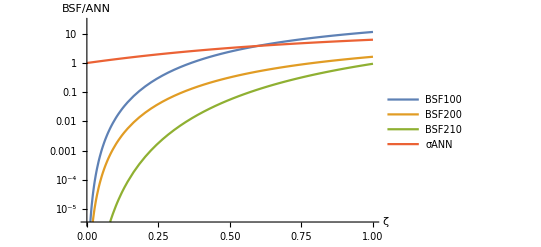

```mathematica
dR=1;
dAdj=1;
IR=1;
IAdj=0;
gχ=4 dR;
σANN=SE[1];
σBSF10=Simplify[((BSF10[1,1]/.s->0)+(BSF10[1,1]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF20=Simplify[((BSF20[1,1]/.s->0)+(BSF20[1,1]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4dR)]];
σBSF21=Simplify[((BSF21[1,1]/.s->0)+(BSF21[1,1]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]];

LogPlot[{σBSF10,σBSF20,σBSF21,σANN},{ζ,0,1},AxesLabel->{"ζ","BSF/ANN"},PlotLegends->{"BSF100","BSF200","BSF210","σANN"}]
```

## Quintuplet MDM

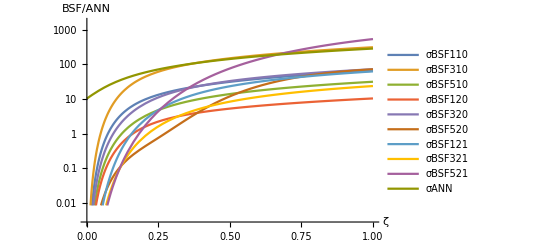

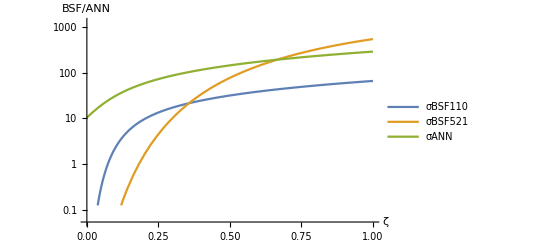

```mathematica
dR=5;
dAdj=3;
IR=10;
IAdj=2;
gχ=2 dR;
σANN=8/gχ^2(30 SE[6]+105/2 SE[3]+(1+1/24)45 SE[5 ]);

σBSF110=Simplify[BSF10[5,6]/.s->0/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF310=Simplify[BSF10[6,5]/.s->1/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]]+Simplify[(BSF10[3,5]/.s->1)/.CJ->Sqrt[21/2]/.Cτ->-Sqrt[42]];
σBSF510=Simplify[BSF10[5,3]/.s->0/.CJ->Sqrt[21/2]/.Cτ->Sqrt[42]]+Simplify[Normal[Series[BSF10[λ,3],{λ,0,0}]]/.s->0/.CJ->Sqrt[12]/.Cτ->-3Sqrt[12]];

σBSF120=Simplify[BSF20[5,6]/.s->0/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF320=Simplify[BSF20[6,5]/.s->1/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]]+Simplify[(BSF20[3,5]/.s->1)/.CJ->Sqrt[21/2]/.Cτ->-Sqrt[42]];
σBSF520=Simplify[BSF20[5,3]/.s->0/.CJ->Sqrt[21/2]/.Cτ->Sqrt[42]]+Simplify[Normal[Series[BSF20[λ,3],{λ,0,0}]]/.s->0/.CJ->Sqrt[12]/.Cτ->-3Sqrt[12]];

σBSF121=Simplify[BSF21[5,6]/.s->1/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF321=Simplify[BSF21[6,5]/.s->0/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]]+Simplify[(BSF21[3,5]/.s->0)/.CJ->Sqrt[21/2]/.Cτ->-Sqrt[42]];
σBSF521=Simplify[BSF21[5,3]/.s->1/.CJ->Sqrt[21/2]/.Cτ->Sqrt[42]]+Simplify[Normal[Series[BSF21[λ,3],{λ,0,0}]]/.s->1/.CJ->Sqrt[12]/.Cτ->-3Sqrt[12]];

(*σBSFI010=Simplify[((BSF10[5,6]/.s->0)+(BSF10[6,5]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSFI020=Simplify[((BSF20[5,6]/.s->0)+(BSF20[6,5]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4dR)]];σBSFI021=Simplify[((BSF21[6,5]/.s->0)+(BSF21[5,6]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4dR)]];σBSFI210=Simplify[((BSF10[5,3]/.s->0)+(BSF10[3,5]/.s->1))/.CJ->Sqrt[21/2]/.Cτ->-Sqrt[42]];
σBSFI220=Simplify[((BSF20[5,3]/.s->0)+(BSF20[3,5]/.s->1))/.CJ->Sqrt[21/2]/.Cτ->-Sqrt[42]];
σBSFI221=Simplify[((BSF21[3,5]/.s->0)+(BSF21[5,3]/.s->1))/.CJ->Sqrt[21/2]/.Cτ->-Sqrt[42]];*)

LogPlot[{σBSF110,σBSF310,σBSF510,σBSF120,σBSF320,σBSF520,σBSF121,σBSF321,σBSF521,σANN},{ζ,0,1},AxesLabel->{"ζ","BSF/ANN"},PlotLegends->{"σBSF110","σBSF310","σBSF510","σBSF120","σBSF320","σBSF520","σBSF121","σBSF321","σBSF521","σANN"}]

LogPlot[{σBSF110,σBSF521,σANN},{ζ,0,1},AxesLabel->{"ζ","BSF/ANN"},PlotLegends->{"σBSF110","σBSF521","σANN"}]
```

Indirect detection (only photon emission)

```mathematica
σBSF310=Simplify[dR^2/5 αem/(3α) BSF10[.00001,5]/.s->1/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]/.ζ->30/.α->1/30/.αem->1/137/.m->10000]+Simplify[(2dR^2)/7 αem/(3α)BSF10[.00001,5]/.s->1/.CJ->Sqrt[21/2]/.Cτ->-Sqrt[42]/.ζ->30/.α->1/30/.αem->1/137/.m->10000]
σBSF320=Simplify[dR^2/5 αem/(3α)BSF20[.00001,5]/.s->1/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]/.ζ->30/.α->1/30/.αem->1/137/.m->10000]+Simplify[(2dR^2)/7 αem/(3α)BSF20[.0001,5]/.s->1/.CJ->Sqrt[21/2]/.Cτ->-Sqrt[42]/.ζ->30/.α->1/30/.αem->1/137/.m->10000]
σBSF321=Simplify[dR^2/5 αem/(3α)BSF21[.00001,5]/.s->0/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]/.ζ->30/.α->1/30/.αem->1/137/.m->10000]+Simplify[(2dR^2)/7 αem/(3α)BSF20[.00001,5]/.s->0/.CJ->Sqrt[21/2]/.Cτ->-Sqrt[42]/.ζ->30/.α->1/30/.αem->1/137/.m->10000]
```

0.0116695

0.106052

8.95901

## Wino MDM

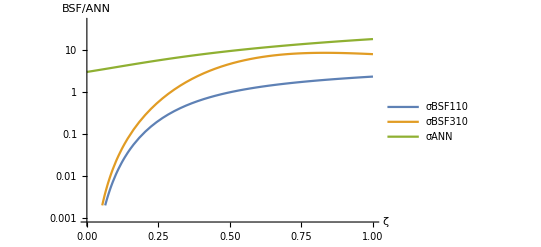

```mathematica
dR=3;
dAdj=3;
IR=2;
IAdj=2;
gχ=2dR;
σANN=8/gχ^2(2 SE[2]+5/2 SE[-1]+(1+1/24)9 SE[1 ]);
σANN0=8/gχ^2(2+5/2+(1+1/24)9 );
σBSFvphoton0=2/3 .22^2(1024 ⅇ^(-4 ζ ArcCot[ζ]) π ζ^5)/(3 (1-ⅇ^(-2 π ζ)) (1+ζ^2)^2);

σBSF110=Simplify[(BSF10[1,2]/.s->0)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF310=Simplify[(BSF10[2,1]/.s->1)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]]+Simplify[(BSF10[-1,1]/.s->1)/.CJ->Sqrt[5/2]/.Cτ->-Sqrt[10]];
σBSF120=Simplify[(BSF20[1,2]/.s->0)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF320=Simplify[(BSF20[2,1]/.s->1)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]]+Simplify[(BSF20[-1,1]/.s->1)/.CJ->Sqrt[5/2]/.Cτ->-Sqrt[10]];
σBSF121=Simplify[(BSF21[1,2]/.s->1)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF321=Simplify[(BSF21[2,1]/.s->0)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]]+Simplify[(BSF21[-1,1]/.s->0)/.CJ->Sqrt[5/2]/.Cτ->-Sqrt[10]];

LogPlot[{Abs[σBSF110],Abs[σBSF310],σANN},{ζ,0,1},AxesLabel->{"ζ","BSF/ANN"},PlotLegends->{"σBSF110","σBSF310","σANN"}]
```

Indirect detection (only photon emission)

```mathematica
σBSF310ind=dR^2/3 αem/(3α)Simplify[Normal[Series[σBSF310/.ζ->α/v,{v,0,0}]],Assumptions->{α>0,v>0}]

σBSF320ind=dR^2/3 αem/(3α)Simplify[Normal[Series[σBSF320/.ζ->α/v,{v,0,0}]],Assumptions->{α>0,v>0}]

σBSF121ind=dR^2/3 αem/(3α)Simplify[Normal[ Series[σBSF321/.ζ->α/v,{v,0,0}]],Assumptions->{α>0,v>0}]
```

(32768 π αem)/(9 ⅇ^8 v)

(4194304 π αem)/(9 ⅇ^16 v)

(765952 π αem)/(3 ⅇ^16 v)

## Gluinos (CJ→6/.Cτ→0 ??)

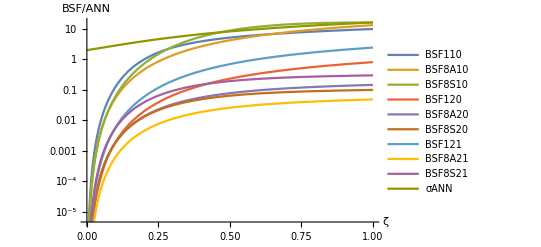

```mathematica
dR=8;
dAdj=8;
IR=3;
IAdj=3;
gχ=2 dR;
σANN=27/32(1/6 SE[3]+1/3 SE[3/2 ]+1/2 SE[-1])+9/8 SE[3/2 ];

σBSF110=Simplify[(BSF10[3/2,3]/.s->0)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF8A10=Simplify[(BSF10[3,3/2]/.s->1)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]]+
Simplify[(BSF10[3/2,3/2]/.s->1)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]]+
Simplify[(BSF10[3,3/2]/.s->1)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF8S10=Simplify[(BSF10[3,3/2]/.s->0)/.CJ->6/.Cτ->0]+Simplify[(BSF10[0.0001,3/2]/.s->0)/.CJ->Sqrt[12]/.Cτ->Sqrt[27]];

σBSF120=Simplify[(BSF20[3/2,3]/.s->0)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF8A20=Simplify[(BSF20[3,3/2]/.s->1)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF8S20=Simplify[(BSF20[3,3/2]/.s->0)/.CJ->6/.Cτ->0];

σBSF121=Simplify[(BSF20[3/2,3]/.s->1)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF8A21=Simplify[(BSF20[3,3/2]/.s->0)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF8S21=Simplify[(BSF20[3,3/2]/.s->1)/.CJ->6/.Cτ->0];

LogPlot[{σBSF110,σBSF8A10,σBSF8S10,σBSF120,σBSF8A20,σBSF8S20,σBSF121,σBSF8A21,σBSF8S21,σANN},{ζ,0,1},AxesLabel->{"ζ","BSF/ANN"},PlotLegends->{"BSF110","BSF8A10","BSF8S10","BSF120","BSF8A20","BSF8S20","BSF121","BSF8A21","BSF8S21","σANN"}]
```

## Squarks

3

8

1/2

3

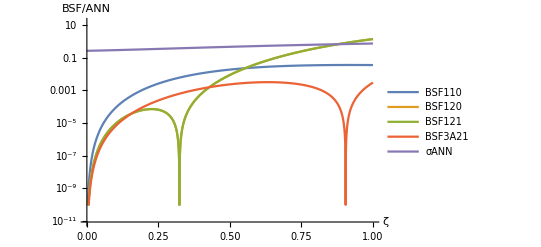

```mathematica
dR=3
dAdj=8
IR=1/2
IAdj=3
σANN=7/27(2/7 SE[4/3]+5/7 SE[-1/6 ]);

σBSF110=Simplify[(BSF10[-1/6,4/3]/.s->0)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]/.gχ->2 dR];
σBSF120=Simplify[(BSF20[-1/6,4/3]/.s->0)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]/.gχ->2 dR];
σBSF121=Simplify[(BSF20[-1/6,4/3]/.s->0)/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->-Sqrt[(IR dAdj IAdj^2)/(4 dR)]/.gχ->2 dR];
σBSF3A21=1/2Simplify[(BSF20[-1/3,2/3]/.s->0)/.CJ->Sqrt[3]/.Cτ->-Sqrt[3]/.gχ->dR];
LogPlot[{σBSF110,σBSF120,σBSF121,σBSF3A21,σANN},{ζ,0,1},AxesLabel->{"ζ","BSF/ANN"},PlotLegends->{"BSF110","BSF120","BSF121","BSF3A21","σANN"}]
```

## Dark SU(3)

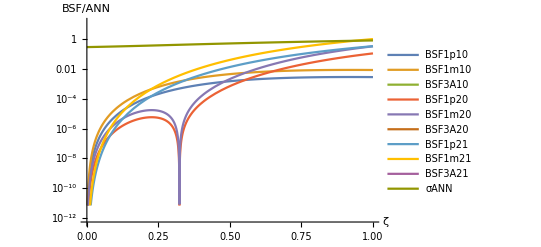

```mathematica
dR=3;
σANN=(7/162+37/72 α22/αDC2)(2/7 SE[4/3]+5/7 SE[-1/6 ]);

σBSF1p10=1/3 Simplify[(BSF10[-1/6,4/3]/.s->0)/.CJ->Sqrt[4/3]/.Cτ->-Sqrt[3]/.gχ->4 dR];
σBSF1m10=1/3 Simplify[(BSF10[-1/6,4/3]/.s->1)/.CJ->Sqrt[4/3]/.Cτ->-Sqrt[3]/.gχ->4 dR];
σBSF3A10=0 1/(2 3)Simplify[(BSF10[-1/3,2/3]/.s->1)/.CJ->Sqrt[3]/.Cτ->-Sqrt[3]/.gχ->2 dR];

σBSF1p20=1/3 Simplify[(BSF20[-1/6,4/3]/.s->0)/.CJ->Sqrt[4/3]/.Cτ->-Sqrt[3]/.gχ->4 dR];
σBSF1m20=1/3 Simplify[(BSF20[-1/6,4/3]/.s->1)/.CJ->Sqrt[4/3]/.Cτ->-Sqrt[3]/.gχ->4 dR];
σBSF3A20=0 1/(2 3)Simplify[(BSF20[-1/3,2/3]/.s->1)/.CJ->Sqrt[3]/.Cτ->-Sqrt[3]/.gχ->2 dR];

σBSF1p21=1/3 Simplify[(BSF21[-1/6,4/3]/.s->0)/.CJ->Sqrt[4/3]/.Cτ->-Sqrt[3]/.gχ->4 dR];
σBSF1m21=1/3 Simplify[(BSF21[-1/6,4/3]/.s->1)/.CJ->Sqrt[4/3]/.Cτ->-Sqrt[3]/.gχ->4 dR];
σBSF3A21=0 1/(2 3)Simplify[(BSF21[-1/3,2/3]/.s->0)/.CJ->Sqrt[3]/.Cτ->-Sqrt[3]/.gχ->2 dR];


LogPlot[{σBSF1p10,σBSF1m10,σBSF3A10,σBSF1p20, σBSF1m20,σBSF3A20,σBSF1p21,σBSF1m21,σBSF3A21,σANN/.α22->1/2αDC2},{ζ,0,1},AxesLabel->{"ζ","BSF/ANN"},PlotLegends->{"BSF1p10","BSF1m10","BSF3A10","BSF1p20","BSF1m20","BSF3A20","BSF1p21","BSF1m21","BSF3A21","σANN"}]
```

# Relic Abundance

```mathematica
BR[Eb_,σv_,Γ_]:=1/(1+Exp[-Eb/T] gDM gSM (π/2)^(3/2) (σv (m T)^(3/2))/Γ)
```

# Cross-checks

```mathematica
μ=m/2;
ω=μ/2 v^2(1+(λf ξ)^2);
Eb=(λf α)^2 μ/2;
a=1/(λf α μ);
v=α/ξ;
Ellisσv=Simplify[3 4 1/8 1/2 (2^9 π^2)/3 α a^2 Eb^4/ω^4 (1+(λi ξ)^2)/(1+(λf ξ)^2) Exp[-4 λi ξ ArcCot[λf ξ]]/(1-Exp[-2π λi ξ])λi/λf   (2 ω^2)/(16 (μ v)^2) v/.λi->3/2/.λf->3]
PetrakifromEllis=Simplify[(2^9 π^2)/3 α a^2 Eb^4/ω^4 (1+(λi ξ)^2)/(1+(λf ξ)^2) Exp[-4 λi ξ ArcCot[λf ξ]]/(1-Exp[-2π λi ξ])λi/λf   (2 ω^2)/(2(μ v)^2) v/.λi->1/.λf->1]
Ellis=Simplify[1/gχ^2(2 s+1)(2^12 π)/3 ⅇ^(-4 λi ζ ArcCot[λf ζ])/(1-ⅇ^(-2 π λi ζ))(λi λf^5  ζ^5 (1+λi^2 ζ^2))/((1+λf^2 ζ^2)^3)C/.s->0/.gχ->16/.λi->3/2/.λf->3/.C->3]
Petraki=Simplify[1/gχ^2(2 s+1)(2^12 π)/3 ⅇ^(-4 λi ζ ArcCot[λf ζ])/(1-ⅇ^(-2 π λi ζ))(λi λf^5  ζ^5 (1+λi^2 ζ^2))/((1+ λf^2 ζ^2)^3)C/.s->0/.gχ->4/.λi->1/.λf->1/.C->1]
```

(1458 ⅇ^(3 ξ (π-2 ArcCot[3 ξ])) π^2 α^2 ξ^5 (4+9 ξ^2))/((-1+ⅇ^(3 π ξ)) m^2 (1+9 ξ^2)^3)

(512 ⅇ^(-4 ξ ArcCot[ξ]) π^2 α^2 ξ^5)/(3 (1-ⅇ^(-2 π ξ)) m^2 (1+ξ^2)^2)

(1458 ⅇ^(3 ζ (π-2 ArcCot[3 ζ])) π ζ^5 (4+9 ζ^2))/((-1+ⅇ^(3 π ζ)) (1+9 ζ^2)^3)

(256 ⅇ^(-4 ζ ArcCot[ζ]) π ζ^5)/(3 (1-ⅇ^(-2 π ζ)) (1+ζ^2)^2)

```mathematica
σ0=(π α^2)/m^2;
SE[λ_]:=(2π λ ζ)/(1-Exp[-2π λ ζ])
(*BSF[λi_,λf_]:=1/gχ^2(2 s+1)(2^12 π)/3(ⅇ^(-4 ξ ArcCot[(λf ξ)/λi])   ξ^5 (1+ξ^2))/((1-ⅇ^(-2 π ξ)) (1+λf^2/λi^2 ξ^2)^3)λf^5/λi^4(dAdj IR)/dR*)
BSF10[λi_,λf_]:=1/gχ^2(2 s+1)(2^12 π)/3 ⅇ^(-4 λi ζ ArcCot[λf ζ])/(1-ⅇ^(-2 π λi ζ))(λi λf^5  ζ^5 (1+λi^2 ζ^2))/((1+λf^2 ζ^2)^3)(C1+C2/λf)^2
BSF20[λi_,λf_]:=(1/gχ^2(2 s+1)(2^15 π)/3(ⅇ^(2 ζ λi (π-2 ArcCot[(ζ λf)/2]))  ζ^5 λf^3 λi (1+ζ^2 λi^2) (C1 λf (4-ζ^2 λf (λf-2 λi))+C2 (4+ζ^2 λf (-3 λf+4 λi)))^2)/((-1+ⅇ^(2 π ζ λi)) (4+ζ^2 λf^2)^5))
BSF21[λi_,λf_]:=(1/gχ^2(2 s+1)(2^13 π)/3 1/((-1+ⅇ^(2 π ζ λi)) (4+ζ^2 λf^2)^5) ⅇ^(2 ζ λi (π-2 ArcCot[(ζ λf)/2]))  ζ^7 λf^5 λi (176 C2^2-192 C1 C2 λf+64 C1^2 λf^2-8 C2^2 ζ^2 λf^2+16 C1 C2 ζ^2 λf^3+3 C2^2 ζ^4 λf^4+2 (-4 C2 ζ^2 λf+C1 (-4+ζ^2 λf^2)) (8 C1 λf+C2 (-4+3 ζ^2 λf^2)) λi+(-32 C1 C2 ζ^2 λf (2+ζ^2 λf^2)+64 C2^2 ζ^2 (3+ζ^2 λf^2)+C1^2 (48+8 ζ^2 λf^2+3 ζ^4 λf^4)) λi^2-8 ζ^2 (2 C2-C1 λf) (4 C2 ζ^2 λf+C1 (4-ζ^2 λf^2)) λi^3+16 ζ^4 (-2 C2+C1 λf)^2 λi^4))
BSF10new[λi_,λf_]:=(1024 π (1+2 s) α^2 ζ^4 λf^3 (2 Cτ+√2 CJ λf)^2 (1-ⅈ ζ λf)^(ⅈ ζ λi) (1+ⅈ ζ λf)^(-ⅈ ζ λi) (-ⅈ+ζ λf)^(-ⅈ ζ λi) (ⅈ+ζ λf)^(ⅈ ζ λi) Gamma[2-ⅈ ζ λi] Gamma[2+ⅈ ζ λi])/(3 gχ^2 m^2 (1+ζ^2 λf^2)^3)/σ0
BSF20new[λi_,λf_]:=(1/gχ^2(2 s+1)(2^15 π)/3(ⅇ^(2 ζ λi (π-2 ArcCot[(ζ λf)/2]))  ζ^5 λf^3 λi (1+ζ^2 λi^2) (CJ λf (4-ζ^2 λf (λf-2 λi))+√2 Cτ (4+ζ^2 λf (-3 λf+4 λi)))^2)/((-1+ⅇ^(2 π ζ λi)) (4+ζ^2 λf^2)^5))
BSF21new[λi_,λf_]:=Simplify[(2^13 π^2 α^2)/(9 gχ^2 m^2 (4+ζ^2 λf^2)^5)ⅇ^(-4 ζ λi  ArcCot[(ζ λf)/2])/(1-ⅇ^(-2 π λi ζ)) (1+2 s)  ζ^7 λf^5  λi (CJ (-12 λi+λf (8+ζ^2 (3 λf-4 λi) λi))+√2 Cτ (4+ζ^2 (-3 λf^2+12 λf λi-8 λi^2)))^2 +(2^18 π^2 α^2)/(9 gχ^2 m^2 (4+ζ^2 λf^2)^5) ⅇ^(-4 ζ λi  ArcCot[(ζ λf)/2])/(1-ⅇ^(-2 π λi ζ))(1+2 s) ζ^7 λf^5 λi (2 √2 Cτ+CJ λf)^2  (1+ζ^2 λi^2) (4+ζ^2 λi^2)]/σ0
```

## Petraki

1

1

1

0

4

(2 π ζ)/(1-ⅇ^(-2 π ζ))

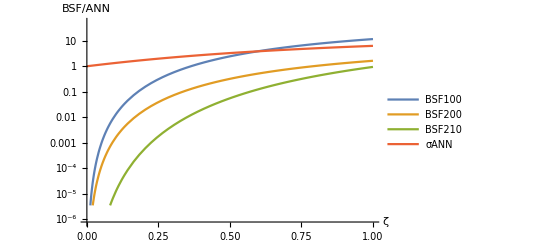

1.

1.

1.

```mathematica
dR=1
dAdj=1
IR=1
IAdj=0
gχ=4 dR
σANN=SE[1]
σBSF10=Simplify[((BSF10[1,1]/.s->0)+(BSF10[1,1]/.s->1))/.C1->Sqrt[(IR dAdj)/dR]/.C2->Sqrt[(IR dAdj IAdj^2)/(2 dR)]];
σBSF20=Simplify[((BSF20[1,1]/.s->0)+(BSF20[1,1]/.s->1))/.C1->Sqrt[(IR dAdj)/dR]/.C2->Sqrt[(IR dAdj IAdj^2)/(2 dR)]];
σBSF21=Simplify[((BSF21[1,1]/.s->0)+(BSF21[1,1]/.s->1))/.C1->Sqrt[(IR dAdj)/dR]/.C2->Sqrt[(IR dAdj IAdj^2)/(2 dR)]];
LogPlot[{σBSF10,σBSF20,σBSF21,σANN},{ζ,0,1},AxesLabel->{"ζ","BSF/ANN"},PlotLegends->{"BSF100","BSF200","BSF210","σANN"}]

σBSF10new=Simplify[((BSF10new[1,1]/.s->0)+(BSF10new[1,1]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSF20new=Simplify[((BSF20new[1,1]/.s->0)+(BSF20new[1,1]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4dR)]];
σBSF21new=Simplify[((BSF21new[1,1]/.s->0)+(BSF21new[1,1]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]];

N[σBSF10/Abs[σBSF10new]/.ζ->.3]
N[σBSF20/Abs[σBSF20new]/.ζ->.3]
N[σBSF21/Abs[σBSF21new]/.ζ->.3]
```

## Quintuplet MDM

5

3

10

2

10

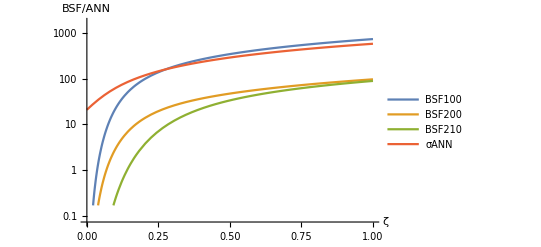

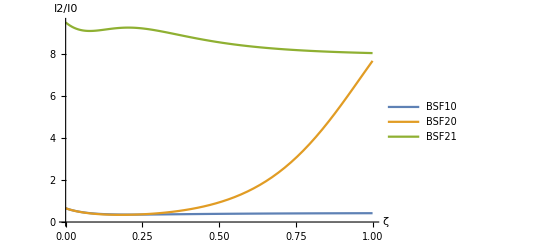

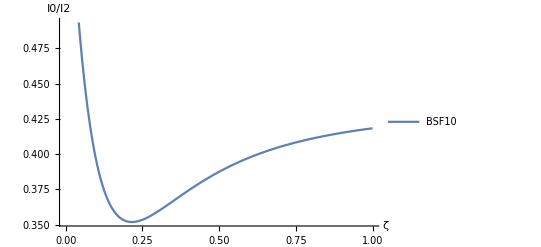

1.+1.12277×10^-17 ⅈ

1.

0.145459

1.-7.24134×10^-17 ⅈ

1.

0.0159133

```mathematica
dR=5
dAdj=3
IR=10
IAdj=2
gχ=2 dR
σANN=16/gχ^2(30 SE[6]+105/2 SE[3]+(1+1/24)45 SE[5 ]);
σBSFI010=Simplify[((BSF10[5,6]/.s->0)+(BSF10[6,5]/.s->1))/.C1->Sqrt[(IR dAdj)/dR]/.C2->Sqrt[(IR dAdj IAdj^2)/(2 dR)]];
σBSFI020=Simplify[((BSF20[5,6]/.s->0)+(BSF20[6,5]/.s->1))/.C1->Sqrt[(IR dAdj)/dR]/.C2->Sqrt[(IR dAdj IAdj^2)/(2 dR)]];
σBSFI021=Simplify[((BSF21[6,5]/.s->0)+(BSF21[5,6]/.s->1))/.C1->Sqrt[(IR dAdj)/dR]/.C2->Sqrt[(IR dAdj IAdj^2)/(2 dR)]];
σBSFI210=Simplify[((BSF10[5,3]/.s->0)+(BSF10[3,5]/.s->1))/.C1->Sqrt[21/2]/.C2->Sqrt[84]];
σBSFI220=Simplify[((BSF20[5,3]/.s->0)+(BSF20[3,5]/.s->1))/.C1->Sqrt[21/2]/.C2->Sqrt[84]];
σBSFI221=Simplify[((BSF21[3,5]/.s->0)+(BSF21[5,3]/.s->1))/.C1->Sqrt[21/2]/.C2->Sqrt[84]];
LogPlot[{σBSFI010,σBSFI020,σBSFI021,σANN},{ζ,0,1},AxesLabel->{"ζ","BSF/ANN"},PlotLegends->{"BSF100","BSF200","BSF210","σANN"}]
Plot[{σBSFI010/σBSFI210,σBSFI020/σBSFI220,σBSFI021/σBSFI221},{ζ,0,1},AxesLabel->{"ζ","I2/I0"},PlotLegends->{"BSF10","BSF20","BSF21"}]
Plot[{σBSFI010/σBSFI210},{ζ,0,1},AxesLabel->{"ζ","I0/I2"},PlotLegends->{"BSF10"}]


σBSFI010new=Simplify[((BSF10new[5,6]/.s->0)+(BSF10new[6,5]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4 dR)]];
σBSFI020new=Simplify[((BSF20new[5,6]/.s->0)+(BSF20new[6,5]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4dR)]];
σBSFI021new=Simplify[((BSF21new[6,5]/.s->0)+(BSF21new[5,6]/.s->1))/.CJ->Sqrt[(IR dAdj)/dR]/.Cτ->Sqrt[(IR dAdj IAdj^2)/(4dR)]];

σBSFI210new=Simplify[((BSF10new[5,3]/.s->0)+(BSF10new[3,5]/.s->1))/.CJ->Sqrt[21/2]/.Cτ->Sqrt[84/2]];
σBSFI220new=Simplify[((BSF20new[5,3]/.s->0)+(BSF20new[3,5]/.s->1))/.CJ->Sqrt[21/2]/.Cτ->Sqrt[84/2]];
σBSFI221new=Simplify[((BSF21new[3,5]/.s->0)+(BSF21new[5,3]/.s->1))/.CJ->Sqrt[21/2]/.Cτ->Sqrt[84/2]];

N[σBSFI010/σBSFI010new/.ζ->.3]
N[σBSFI020/σBSFI020new/.ζ->.3]
N[σBSFI021/σBSFI021new/.ζ->.3]
N[σBSFI210/σBSFI210new/.ζ->.3]
N[σBSFI220/σBSFI220new/.ζ->.3]
N[σBSFI221/σBSFI221new/.ζ->.3]
```

```mathematica
CJ->Sqrt[(IR dAdj)/dR]
Cτ->Sqrt[(IR dAdj IAdj^2)/(8 dR)]
```

CJ→√2

Cτ→1